```mathematica
Clear[axk,ayk,k,ax,ay,bx,by,qx,qy]
Integrate[(1-(x/a)^2)^2 Exp[ⅈ k x],{x,-a,a},Assumptions->Im[a]==0 && a>0]
```

-(16 (3 a k Cos[a k]+(-3+a^2 k^2) Sin[a k]))/(a^4 k^5)

```mathematica
xS = %;
```

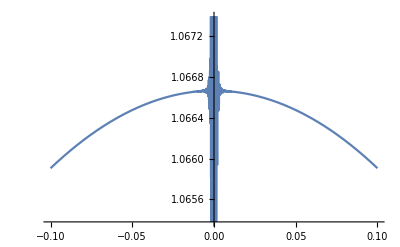

16/15

```mathematica
Clear[a];
a = 1;
Plot[xS,{k,-0.1,0.1}]
Limit[xS,k->0]
```

```mathematica
xS
```

-(16 (3 k Cos[k]+(-3+k^2) Sin[k]))/k^5

```mathematica
Series[xS,{k,0,6}]
```

16/15-(8 k^2)/105+(2 k^4)/945-k^6/31185+O[k]^7

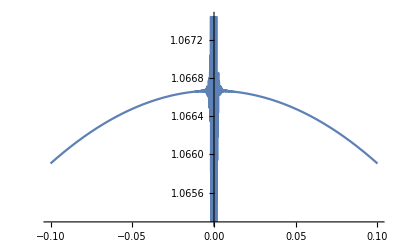
```mathematica
ReplaceAll[xS,{Cos[k] -> 1-k^2 /2 + k^4 / 24 - k^6 / (30*24)}]
-(16 (3 k (1-k^2/2+k^4/24-k^6/720)+(-3+k^2) Sin[k]))/k^5
xSS = ReplaceAll[%, {Sin[k] -> k-k^3 /6 + k^5 / 120 - k^7 / (42*120)}]
-(16 (3 k (1-k^2/2+k^4/24-k^6/720)+(-3+k^2) (k-k^3/6+k^5/120-k^7/5040)))/k^5
Plot[xSS,{k,-0.1,0.1}]
-Graphics-
FullSimplify[xSS]
1/315 (336-24 k^2+k^4)
```

#### Using the Bouwkamp definition for impedance; Power/v^2 Power emitted by the radiator at z=0 plane is the integral of p(x,y)*v(x,y) ds over x-y plane leads to the square of the fourier transform of the deflection profile in the integrand = S^2(kx,ax,bx) * S^2(ky,ay,by) where S(k,a,b) is 1D FT of one of the dimensions of the deflection profile - defined in the notes S(kx,ax,bx)/bx = xS below; q=a/b

```mathematica
xS=((-8/x)((1/(x^2) + 6/(x^4) + (2/5)*(SphericalBesselY[3,x]+SphericalBesselY[1,x]))*Sin[qx*x] + (-2/5)*(SphericalBesselJ[3,x] + SphericalBesselJ[1,x])*Cos[qx*x]))^2;
```

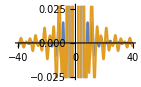
```mathematica
(*qx=1;
Plot[{xS[x,qx], 3.0671312295349495 Sinc[1.5355271144573683 x] Sinc[0.37611190490493007 x]},{x,-40,40}]*)
-Graphics-
(*
Clear[a,b,qx]
qx=1;
pnts=Table[{x,Re[xS[x,qx]]},{x,-5,5,0.015}]//N;
ListPlot[%]
FindFit[pnts,a Sinc[b x] Sinc[d x],{a,b,c,d},x]
(*
Table[{qx,FindFit[Table[Re[xS[x,qx]],{x,-5,5,0.015}]//N,a Sinc[b x],{a,b},x]},{qx,{1,2,3,4,5,6,7,8,9,10}}]*)*)
-Graphics-
{a->3.0671312295349495,b->1.5355271144573683,c->1.,d->0.37611190490493007}
```

Using the first identity listed here: https://dlmf.nist.gov/10.51
The following is equivalent to the expression above

```mathematica
xSs=(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2;
(*qx=2;
NIntegrate[Abs[xS-xSs],{x,-50,50}]
Plot[{xS,xSs},{x,-5,5}]*)
```

64 (-2/5 Cos[qx x] (1/3 SphericalBesselJ[0,x]+10/21 SphericalBesselJ[2,x]+1/7 SphericalBesselJ[4,x])+Sin[qx x] (6/x^5+1/x^3+2/5 (1/3 SphericalBesselY[0,x]+10/21 SphericalBesselY[2,x]+1/7 SphericalBesselY[4,x])))^2

The impedance is then the integral of “S^2(kx,ax,bx) S^2(ky,ay,by) 1/kz dkx dky“ over kx and ky from -inf to inf
with the coefficient \frac{k\rho c v^2_0 }{4\pi^2} b^2_x b^2_y
	After change of variables the integrand will be: “S^2(k t cos(phi),ax,bx) S^2(k t sin(phi),ay,by) t dt dphi / sqrt(1-t^2)”
	with the coefficient: \frac{k^2 \rho c v^2_0 }{4\pi^2} b^2_x b^2_y * (1/V_ref)^2

```mathematica
xOrig=(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2
xOrig=ReplaceAll[xOrig,x->(bxk*t*Cos[ϕ])];
yOrig=(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2;
yOrig=ReplaceAll[yOrig,qx->qy];
yOrig=ReplaceAll[yOrig,x->(byk*t*Sin[ϕ])];
```

64 (-2/5 Cos[qx x] (1/3 SphericalBesselJ[0,x]+10/21 SphericalBesselJ[2,x]+1/7 SphericalBesselJ[4,x])+Sin[qx x] (6/x^5+1/x^3+2/5 (1/3 SphericalBesselY[0,x]+10/21 SphericalBesselY[2,x]+1/7 SphericalBesselY[4,x])))^2

```mathematica
Series[(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2,{x,0,8}]
```

4/225 (8+15 qx)^2-(4 ((8+15 qx) (8+35 qx+56 qx^2+35 qx^3)) x^2)/1575+64 (((8+35 qx+56 qx^2+35 qx^3)^2)/705600+2 (-2/15-qx/4) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) x^4+64 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-2/15-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))) x^6+64 ((-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-2/15-qx/4) (-qx/2419200-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) x^8+O[x]^9

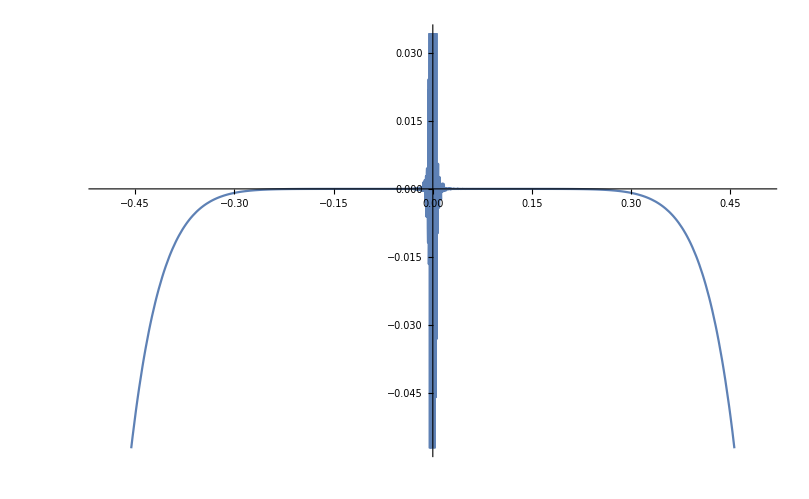

```mathematica
qx=2;
tempo=(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2;
tempx=4/225 (8+15 qx)^2-(4 ((8+15 qx) (8+35 qx+56 qx^2+35 qx^3)) x^2)/1575+64 (((8+35 qx+56 qx^2+35 qx^3)^2)/705600+2 (-2/15-qx/4) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) x^4+64 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-2/15-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))) x^6+64 ((-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-2/15-qx/4) (-qx/2419200-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) x^8;
Plot[{100*tempo-100*tempx},{x,-0.5,0.5}]
```

```mathematica
xApprox=4/225 (8+15 qx)^2-(4 ((8+15 qx) (8+35 qx+56 qx^2+35 qx^3)) x^2)/1575+64 (((8+35 qx+56 qx^2+35 qx^3)^2)/705600+2 (-2/15-qx/4) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) x^4+64 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-2/15-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))) x^6+64 ((-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-2/15-qx/4) (-qx/2419200-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) x^8;
(*xApprox=ReplaceAll[xApprox,qx->(ax/bx)];*)
xApprox=ReplaceAll[xApprox,x->(bxk*t*Cos[ϕ])];

yApprox=4/225 (8+15 qx)^2-(4 ((8+15 qx) (8+35 qx+56 qx^2+35 qx^3)) x^2)/1575+64 (((8+35 qx+56 qx^2+35 qx^3)^2)/705600+2 (-2/15-qx/4) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) x^4+64 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-2/15-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))) x^6+64 ((-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-2/15-qx/4) (-qx/2419200-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) x^8;
(*yApprox=ReplaceAll[yApprox,qx->(ay/by)];*)
yApprox=ReplaceAll[yApprox,qx->qy];
yApprox=ReplaceAll[yApprox,x->(byk*t*Sin[ϕ])];
```

4/225 (8+15 qy)^2-(4 byk^2 (8+15 qy) (8+35 qy+56 qy^2+35 qy^3) t^2 Sin[ϕ]^2)/1575+64 byk^4 (((8+35 qy+56 qy^2+35 qy^3)^2)/705600+2 (-2/15-qy/4) (-qy/576-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))) t^4 Sin[ϕ]^4+64 byk^6 (1/420 (8+35 qy+56 qy^2+35 qy^3) (-qy/576-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))+2 (-2/15-qy/4) (qy/28800+qy^3/3456+qy^5/2880+qy^7/20160-2/5 (-1/99792-qy^2/3024-qy^4/1008-qy^6/2160))) t^6 Sin[ϕ]^6+64 byk^8 ((-qy/576-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))^2+1/420 (8+35 qy+56 qy^2+35 qy^3) (qy/28800+qy^3/3456+qy^5/2880+qy^7/20160-2/5 (-1/99792-qy^2/3024-qy^4/1008-qy^6/2160))+2 (-2/15-qy/4) (-qy/2419200-qy^3/172800-qy^5/69120-qy^7/120960-qy^9/1451520-2/5 (1/10378368+qy^2/199584+qy^4/36288+qy^6/30240+qy^8/120960))) t^8 Sin[ϕ]^8

```mathematica
(*axk=1;
ayk=1;
ax=0.003;
ay=0.003;
k=axk/ax;
bx=0.5/k;
by=0.5/k;*)
```

```mathematica
xComplete=Piecewise[{{xApprox,Abs[bxk t Cos[ϕ]]<0.1}},xOrig];
yComplete=Piecewise[{{yApprox,Abs[byk t Sin[ϕ]]<0.1}},yOrig];
```

```mathematica
3600 k^2 *(((ax+bx)^2)/(15 ax+8 bx))*(((ay+by)^2)/(15 ay+8 by))*(Pi^(-2)) NIntegrate[(t/Sqrt[1-t^2])*xPart*yPart,{t,0,1},{ϕ,0,2 Pi}]
```

0.93257

```mathematica
Plot3D[(t/Sqrt[1-t^2])*xPart*yPart,{t,0,1},{ϕ,0,Pi/2},PlotStyle->Directive[RGBColor[0.92,0.96,0.96],Opacity[0.85]],Mesh->All,MeshFunctions->Automatic]
```

-Graphics3D-

### Reactance

```mathematica
-3600 k^2 *(((ax+bx)^2)/(15 ax+8 bx))*(((ay+by)^2)/(15 ay+8 by))*(Pi^(-2)) NIntegrate[(t/Sqrt[t^2-1])*xPart*yPart,{t,1,∞},{ϕ,0,2 Pi}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-0.722398

### Coding with Mathematica

```mathematica
Clear[axk,ayk,k,ax,ay,bx,by,qx,qy]
```

```mathematica
xOriginal[bxk_,qx_]:=64 (-(2/5) Cos[bxk qx t Cos[ϕ]] (1/3 SphericalBesselJ[0,bxk t Cos[ϕ]]+10/21 SphericalBesselJ[2,bxk t Cos[ϕ]]+1/7 SphericalBesselJ[4,bxk t Cos[ϕ]])+Sin[bxk qx t Cos[ϕ]] (Sec[ϕ]^3/(bxk^3 t^3)+(6 Sec[ϕ]^5)/(bxk^5 t^5)+2/5 (1/3 SphericalBesselY[0,bxk t Cos[ϕ]]+10/21 SphericalBesselY[2,bxk t Cos[ϕ]]+1/7 SphericalBesselY[4,bxk t Cos[ϕ]])))^2
yOriginal[byk_,qy_]:=64 (-(2/5) Cos[byk qy t Sin[ϕ]] (1/3 SphericalBesselJ[0,byk t Sin[ϕ]]+10/21 SphericalBesselJ[2,byk t Sin[ϕ]]+1/7 SphericalBesselJ[4,byk t Sin[ϕ]])+Sin[byk qy t Sin[ϕ]] (Csc[ϕ]^3/(byk^3 t^3)+(6 Csc[ϕ]^5)/(byk^5 t^5)+2/5 (1/3 SphericalBesselY[0,byk t Sin[ϕ]]+10/21 SphericalBesselY[2,byk t Sin[ϕ]]+1/7 SphericalBesselY[4,byk t Sin[ϕ]])))^2
xApproximate[bxk_,qx_]:=4/225 (8+15 qx)^2-(4 bxk^2 (8+15 qx) (8+35 qx+56 qx^2+35 qx^3) t^2 Cos[ϕ]^2)/1575+64 bxk^4 ((8+35 qx+56 qx^2+35 qx^3)^2/705600+2 (-(2/15)-qx/4) (-(qx/576)-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) t^4 Cos[ϕ]^4+64 bxk^6 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-(qx/576)-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-(2/15)-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-(1/99792)-qx^2/3024-qx^4/1008-qx^6/2160))) t^6 Cos[ϕ]^6+64 bxk^8 ((-(qx/576)-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-(1/99792)-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-(2/15)-qx/4) (-(qx/2419200)-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) t^8 Cos[ϕ]^8
yApproximate[byk_,qy_]:=4/225 (8+15 qy)^2-(4 byk^2 (8+15 qy) (8+35 qy+56 qy^2+35 qy^3) t^2 Sin[ϕ]^2)/1575+64 byk^4 ((8+35 qy+56 qy^2+35 qy^3)^2/705600+2 (-(2/15)-qy/4) (-(qy/576)-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))) t^4 Sin[ϕ]^4+64 byk^6 (1/420 (8+35 qy+56 qy^2+35 qy^3) (-(qy/576)-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))+2 (-(2/15)-qy/4) (qy/28800+qy^3/3456+qy^5/2880+qy^7/20160-2/5 (-(1/99792)-qy^2/3024-qy^4/1008-qy^6/2160))) t^6 Sin[ϕ]^6+64 byk^8 ((-(qy/576)-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))^2+1/420 (8+35 qy+56 qy^2+35 qy^3) (qy/28800+qy^3/3456+qy^5/2880+qy^7/20160-2/5 (-(1/99792)-qy^2/3024-qy^4/1008-qy^6/2160))+2 (-(2/15)-qy/4) (-(qy/2419200)-qy^3/172800-qy^5/69120-qy^7/120960-qy^9/1451520-2/5 (1/10378368+qy^2/199584+qy^4/36288+qy^6/30240+qy^8/120960))) t^8 Sin[ϕ]^8
```

```mathematica
xPartInt[bxk_,qx_]:=Piecewise[{{xApproximate[bxk,qx],Abs[bxk t Cos[ϕ]]<0.1}},xOriginal[bxk,qx]]
yPartInt[byk_,qy_]:=Piecewise[{{yApproximate[byk,qy],Abs[byk t Sin[ϕ]]<0.1}},yOriginal[byk,qy]]
```

```mathematica
byk[bxk_,qx_,qxy_,qy_]:=(bxk/qxy) (1+qx)/(1+qy)
ayk[bxk_,qx_,qxy_,qy_]:=qy (bxk/qxy) (1+qx)/(1+qy)
zR[bxk_,qx_,qxy_,qy_]:=bxk^2 (byk[bxk,qx,qxy,qy])^2 /(4 (315 qx bxk+128 bxk) (315 (ayk[bxk,qx,qxy,qy])+128 (byk[bxk,qx,qxy,qy]))/99225) ((4 Pi^2)^(-1))  NIntegrate[(t/Sqrt[1-t^2])*xPartInt[bxk,qx]*yPartInt[byk[bxk,qx,qxy,qy],qy],{t,0,1},{ϕ,0,2Pi}];zI[bxk_,qx_,qxy_,qy_]:=bxk^2 (byk[bxk,qx,qxy,qy])^2 /(4 (315 qx bxk+128 bxk) (315 (ayk[bxk,qx,qxy,qy])+128 (byk[bxk,qx,qxy,qy]))/99225) ((4 Pi^2)^(-1))  NIntegrate[(t/Sqrt[t^2-1])*xPartInt[bxk,qx]*yPartInt[byk[bxk,qx,qxy,qy],qy],{t,1,∞},{ϕ,0,2Pi}];
```

The results are essentially: P_tot/(ρ c v_R^2 S_0)
	So they are dimensionless
Example of a calculation:
First, run all the cells below “Coding with Mathematica” subsection, then, run the cell below as the example. Ignore the warnings

```mathematica
Monitor[Table[{10^i,j,r,j,zR[10^i/(1+0.01),j,1/r,j],zI[10^i/(1+0.01),j,1/r,j]},{i,-1,1,0.02},{j,{0.01}},{r,{1,5,10, 15, 20, 25, 30}}],i]
dat=%;
Export["erics.txt",dat,"Table","FieldSeparators"->","]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 9.13301 and 0.000766253 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 8.57063 and 0.000737125 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 8.04366 and 0.000709621 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{1.,1.},{6.18907456524075323678335536214945022948086261749267578125,5.8904862254808616484069716534577310085296630859375}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::zeroregion: Integration region {{1.,1.},{0.0941107,0.392699}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::zeroregion: Integration region {{1.,1.},{0.0140091,0.0941107}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.